#### Problem description

```mathematica
Import["/Users/wenqiangfang/Dropbox (Brown)/Apps/OverLeafGit/StairStep/Figures/BeamSchematic_V10.png"]
```

-Graphics-

The governing equation for the Euler Elastica problem is

E I (d^2 θ)/(d s^2)+P_1 sin(θ)- P_2 cos(θ)=0

where 0≤s≤S is the arc length coordinate, θ is the angle of deflection (in radians) at point s, P_1 (positive when pointing to right) and P_2 (positive when pointing downward) are the horizontal and vertical forces at the left end of the beam, respectively.

We define θ as the angle from (ê)_1 to T̂ in the counter clockwise direction. (counter clockwise direction is the direction from (ê)_1 to (ê)_2.) We should have cos(θ) =T̂·(ê)_1

r(s)=x_1(s)(ê)_1+x_2(s) (ê)_2
T = (d r(s))/(d s)=x_1'(s)(ê)_1+x_2'(s) (ê)_2
||T||=√((x_1')^2+(x_2')^2)=1 (inextensibility)
T̂ =T/||T||=T
T̂·(ê)_1=x_1'(s)=cos(θ(s))
x_2'=sin(θ(s))
T=cos(θ(s))(ê)_1+sin(θ(s))(ê)_2
N=(d T(s))/(d s)=x_1''(s)(ê)_1+x_2''(s) (ê)_2
x_1''(s)=-sin(θ(s))θ'(s)
x_2''(s)=cos(θ(s))θ'(s)
||N|| = √((x_1'')^2+(x_2'')^2)=√((θ'(s))^2)=|θ'(s)| 
N̂=N/||N||=sign(θ'(s))(-sin(θ(s))(ê)_1+cos(θ(s)) (ê)_2)

The external force is P=P_1(ê)_1+P_2(ê)_2=P_n N̂-P_t T̂ and P_t=μ P_n.
In this case sign(θ'(s)) = -1, N̂=sin(θ(s))(ê)_1-cos(θ(s)) (ê)_2

P_1=P_n sin(θ_0)-μ P_n cos(θ_0)
P_2=-(P_n cos(θ_0)+μ P_n sin(θ_0))

Let ξ=2s/S, θ̂(ξ)=θ(s),  k=(P_n S^2)/(4 E I), g(ξ)=θ̂(ξ)-OverHat[θ_0]then the equation becomes

E I (d^2 θ)/(d s^2)+P_n(sin(θ_0)-μ  cos(θ_0))sin(θ)-P_n( cos(θ_0)+μ  sin(θ_0))cos(θ)=0
E I (d^2 θ)/(d s^2)-P_n(-cos(θ-θ_0)+μ  sin(θ-θ_0))=0
(d^2 θ̂(ξ))/(d ξ^2)=S^2/4(d^2 θ)/(d s^2)
(d^2 θ̂(ξ))/(d ξ^2)+k (cos(θ̂-OverHat[θ_0])-μ  sin(θ̂-OverHat[θ_0]))=0
(d^2 g(ξ))/(d ξ^2)+k (cos(g(ξ))-μ  sin(g(ξ)))=0

The simplified governing equation and boundary conditions are as follows

(d^2 g(ξ))/(d ξ^2)+k (cos(g(ξ))-μ  sin(g(ξ)))=0
g(ξ=0)=0
g'(ξ=0)=0
g(ξ=1)=-θ_0

where OverHat[θ_0]=θ̂(ξ=0)=θ(s=0)=θ_0>0, F=-2 P_2>0 is the magnitude of the reaction force.

And we also have

L=S∫_0^1 cos(θ̂(ξ)) dξ=S∫_0^1 cos(g-g(1)) dξ
w_0=S/2∫_0^1 sin(θ̂(ξ)) dξ=S/2∫_0^1 sin(g-g(1)) dξ
(P_n L^2)/(4 E I)=k (L/S)^2=(k(∫_0^1 cos(g-g(1)) dξ))^2
F=-2 P_2=2P_n(cos(θ_0)+μ sin(θ_0))
F̂=(F L^2)/(E I)=2P_n(cos(θ_0)+μ sin(θ_0))L^2/(E I)
= 8(cos(θ_0)+μ sin(θ_0))(P_n L^2)/(4E I)
=8(k(∫_0^1 cos(g-g(1)) dξ))^2(cos(θ_0)+μ sin(θ_0))
(ŵ)_0=w_0/L=1/2(∫_0^1 sin(g-g(1)) dξ)/(∫_0^1 cos(g-g(1)) dξ)

### Analytical solution

For the problem

θ''(s)+P̂ sin(θ(s))=0
θ(0)=0
θ(1)=0

For the current problem

(d^2 g(ξ))/(d ξ^2)+k (cos(g(ξ))-μ  sin(g(ξ)))=0
g(ξ=0)=0
g'(ξ=0)=0
g(ξ=1)=-θ_0

We can write it as equation of β(ξ)=g(ξ)+g_0, where sin(g_0)=1/(√(1+μ^2)),cos(g_0)=-μ/(√(1+μ^2))

(d^2 β(ξ))/(d ξ^2)+k √(1+μ^2) sin(β)=0
β(ξ=0)=g_0=arccos(-μ/(√(1+μ^2)))
β'(ξ=0)=0

```mathematica
β[s_,p_,κ_]=2 ArcSin[√κ JacobiCD[√p s,κ]];
IntCos[p_,κ_]:=1-(2 (√p-EllipticE[JacobiAmplitude[√p,κ],κ]) JacobiDN[√p,κ])/(√p √(1-κ JacobiSN[√p,κ]^2))-(2 √2 κ JacobiCN[√p,κ] JacobiDN[√p,κ] JacobiSN[√p,κ])/(√p √(1-κ JacobiSN[√p,κ]^2) √(2-κ+κ JacobiCN[√p,κ]^2-κ JacobiSN[√p,κ]^2));
IntSin[p_,κ_]:=-((2 (-1+κ JacobiSN[√p,κ]^2)^2 ((-1+κ) EllipticE[ArcSin[(√(2-κ+κ JacobiCN[√p,κ]^2-κ JacobiSN[√p,κ]^2))/(√2)],(-1+JacobiDN[√p,κ]^2/(1-κ JacobiSN[√p,κ]^2))/(-1+κ)] JacobiNS[√p,κ] √(-κ JacobiSN[√p,κ]^2 (-2+κ-κ JacobiCN[√p,κ]^2+κ JacobiSN[√p,κ]^2)) √(1/((-1+κ) (-1+κ JacobiSN[√p,κ]^2))(-κ (-1+JacobiSN[√p,κ]^2) (-1+κ JacobiSN[√p,κ]^2)-JacobiDN[√p,κ]^2 (-2+κ+κ JacobiSN[√p,κ]^2)+κ JacobiCN[√p,κ]^2 (-1+JacobiDN[√p,κ]^2+κ JacobiSN[√p,κ]^2)))-1/(-1+κ JacobiSN[√p,κ]^2)EllipticF[ArcSin[(√(2-κ+κ JacobiCN[√p,κ]^2-κ JacobiSN[√p,κ]^2))/(√2)],(-1+JacobiDN[√p,κ]^2/(1-κ JacobiSN[√p,κ]^2))/(-1+κ)] JacobiNS[√p,κ] √(-κ JacobiSN[√p,κ]^2 (-2+κ-κ JacobiCN[√p,κ]^2+κ JacobiSN[√p,κ]^2)) (JacobiDN[√p,κ]^2+κ (-1+κ JacobiSN[√p,κ]^2)) √(1/((-1+κ) (-1+κ JacobiSN[√p,κ]^2))(-κ (-1+JacobiSN[√p,κ]^2) (-1+κ JacobiSN[√p,κ]^2)-JacobiDN[√p,κ]^2 (-2+κ+κ JacobiSN[√p,κ]^2)+κ JacobiCN[√p,κ]^2 (-1+JacobiDN[√p,κ]^2+κ JacobiSN[√p,κ]^2)))+κ JacobiSN[√p,κ] (κ+((-2+κ) JacobiDN[√p,κ]^2)/(1-κ JacobiSN[√p,κ]^2)-κ (JacobiCN[√p,κ]^2-JacobiSN[√p,κ]^2) (-1+JacobiDN[√p,κ]^2/(1-κ JacobiSN[√p,κ]^2)))))/(√p √κ JacobiDN[√p,κ]^4 (2-κ+κ JacobiCN[√p,κ]^2-κ JacobiSN[√p,κ]^2) √((-κ (-1+JacobiSN[√p,κ]^2) (-1+κ JacobiSN[√p,κ]^2)-JacobiDN[√p,κ]^2 (-2+κ+κ JacobiSN[√p,κ]^2)+κ JacobiCN[√p,κ]^2 (-1+JacobiDN[√p,κ]^2+κ JacobiSN[√p,κ]^2))/(JacobiDN[√p,κ]^2 (2-κ+κ JacobiCN[√p,κ]^2-κ JacobiSN[√p,κ]^2)))));
```

```mathematica
NumSol[μ_,k_]:=Module[{g,solg,gsol,LS,w0S,w0hat,Fhat},solg=NDSolve[{g''[ξ]+k( Cos[g[ξ]]-μ Sin[g[ξ]])==0,g[0]==0,g'[0]==0},g,{ξ,0,1}];
gsol[ξ_]=g[ξ]/.solg[[1]];
LS=NIntegrate[Cos[(gsol[ξ]-gsol[1])],{ξ,0,1}];
w0S=NIntegrate[Sin[(gsol[ξ]-gsol[1])],{ξ,0,1}]/2;
w0hat = w0S/LS;
Fhat = 8k(Cos[-gsol[1]]+μ Sin[-gsol[1]])LS^2;
{k,μ,1/LS,w0hat,Fhat,-gsol[1]}]
```

```mathematica
AnaSol[μ_,k_]:=Module[{p,kn,g0,Solkn,β1,knReal,gsol,LS,w0S,w0hat,Fhat},
p = k Sqrt[1+μ^2];
g0 = ArcCos[-μ/Sqrt[1+μ^2]];
knReal=1/2 (1+μ/(√(1+μ^2)));
β1=β[1,p,knReal];
gsol[s_]=β[s,p,knReal]-g0;
LS = Cos[β1] IntCos[p,knReal]+Sin[β1]IntSin[p,knReal];
w0S = (Cos[β1] IntSin[p,knReal]-Sin[β1]IntCos[p,knReal])/2;
w0hat = w0S/LS;
Fhat = 8k(Cos[-gsol[1]]+μ Sin[-gsol[1]])LS^2;
{k,μ,1/LS,w0hat,Fhat,-gsol[1]}]
```

For the instability point, we have

(d F̂)/(d k)=0
(d(8(k(∫_0^1 cos(g-g(1)) dξ))^2(cos(θ_0)+μ sin(θ_0))))/(d k)=0
k(∫_0^1 cos(g-g(1)) dξ)^2(cos(θ_0)+μ sin(θ_0))+k

### Get saved solution

```mathematica
SetDirectory[NotebookDirectory[]];
Get<<"data/SolutionVector2_Feb3";
SolutionVector3=SolutionVector2/.Null->Nothing;
```

SolutionVector2 = {OverHat[w_0], F̂, k, θ_0, Ŝ, μ}

```mathematica
Outline[text_]:=First@ImportString[ExportString[text,"PDF"],"PDF","TextMode"->"Outlines"]
linearFrameTicks={{Most/@Charting`ScaledTicks[{Identity,Identity}][##]&,Most/@Charting`ScaledFrameTicks[{Identity,Identity}][##]&},{Most/@Charting`ScaledTicks[{Identity,Identity}][##]&,Most/@Charting`ScaledFrameTicks[{Identity,Identity}][##]&}};
```

#### μ0 = 0.5

```mathematica
Lfragf[x_,k_,x0_,y0_]=-k(x-x0)+y0;
```

```mathematica
PlotHyster[μ0i_:0.5,Ai_:0.05,λi_:0.004π,ϕi_:0,OblSlopei_:30]:=Module[{μ0B=μ0i,
Abasis=Ai,
λbasis=λi,
ϕbasis=ϕi,
OblSlope=OblSlopei,
Posμ0B,Endw0,fitFw0B,Levelμ0S,fitSw0B,fitVariation,EndFail},
Posμ0B=μ0B/0.002+1;
Endw0=SolutionVector3[[Posμ0B,-1,1]];
fitFw0B=Module[{data1,fit},
data1=SolutionVector3[[Posμ0B,;;,{1,2}]];
fit[x_]=Fit[data1,{x,x^2,x^3,x^4,x^5,x^6},x];
Function[x,Evaluate@fit[x]]
];
Off[General::partw];
Levelμ0S=Module[{μ0=μ0B,A = Abasis,λ=λbasis,ϕ=ϕbasis,arclength,frictionC,levelset,FwLevelset,Levelμ0},
arclength=SolutionVector3[[;;,;;,5]];
frictionC=SolutionVector3[[;;,;;,6]];
levelset=frictionC-μ0(1+A Cos[2π arclength/λ+ϕ]);
FwLevelset=Flatten[Table[{SolutionVector3[[i,j,1]],SolutionVector3[[i,j,2]],
levelset[[i,j]]},{i,1,Length@SolutionVector3},{j,1,Length[SolutionVector3[[i]]]}],1];
Levelμ0=Select[FwLevelset,Abs[#[[3]]]<10^-3&];
(SortBy[Levelμ0,First])
(*FailIndex=Length@Select[Levelμ0S[[1,;;,1]],0<#≤w0starN[[NTest]]&]+LengthOffset;*)];
fitSw0B=Module[{data1,fit},
data1=SolutionVector3[[Posμ0B,;;,{1,5}]];
fit[x_]=Fit[data1,{1,x,x^2,x^3},x];
Function[x,fit[x]]
];
fitVariation=Module[{ λ=λbasis,ϕ=ϕbasis,xx1,yy1,data1,ABF,p1,p2,Divs,MaxList,Maxyy,Maxxx,MaxPos,fit1},
xx1=fitSw0B/@Levelμ0S[[;;,1]];
yy1=Levelμ0S[[;;,2]]-fitFw0B/@Levelμ0S[[;;,1]];
Divs=Partition[Range[xx1[[1]],xx1[[-1]],λ],2,1];
MaxList =Table[
p1 = Position[xx1,Select[xx1,Divs[[n,1]]≤#<Divs[[n,2]]&][[1]]][[1,1]];
p2 = Position[xx1,Select[xx1,Divs[[n,1]]≤#<Divs[[n,2]]&][[-1]]][[1,1]];
Maxyy = Max[yy1[[p1;;p2]]];
MaxPos=Position[yy1,Maxyy][[1,1]];
Maxxx=xx1[[MaxPos]];
{Maxxx,Abs@Maxyy},
{n,1,Length@Divs}];
fit1[x_]=Fit[MaxList,{1,x,x^2,x^3,x^4,x^5,x^6},x];
Function[x,fit1[x]Cos[2π x/λ+ϕ]]
];
EndFail=0.9Endw0;
Module[{f,ind,IntSecPxSol,IntSecPx,IntSecPxy,IntSecP,LIntSecPxSol,LIntSecPx,LIntSecPxy,LIntSecP,Lfrag,LfragArray,LfragRange,ffragRangeFront,ffragRange,IntSecUx,IntSecUxy,LIntSecUxSol,LIntSecUx,LIntSecUxy,IntSecU,LIntSecU,LfragU,LfragArrayU,LfragRangeU,ffragRangeFrontU,ffragRangeU,ffrag,ffragU},
f[x_]=Simplify[Through[(Composition[fitVariation,fitSw0B]+fitFw0B)[x]]];
IntSecPxSol=NSolve[{f'[x]==-OblSlope,0<x<EndFail},x];
IntSecPx=x/.#&/@IntSecPxSol[[;;;;2]];
IntSecPxy={x,f[x]}/.#&/@IntSecPxSol[[;;;;2]];
LIntSecPxSol=(NSolve[{f[x]==Lfragf[x,OblSlope,IntSecPxy[[#,1]],IntSecPxy[[#,2]]],IntSecPxy[[#,1]]+10^-5<x<EndFail},x][[1]])&/@Range[Length@IntSecPxy];
ind=0;
If[LIntSecPxSol[[-1]]=={}[[1]],ind=1;LIntSecPxSol[[-1]]={x->EndFail}];
LIntSecPx=x/.#&/@LIntSecPxSol;
LIntSecPxy={x,f[x]}/.#&/@LIntSecPxSol;
Lfrag[x_]=({Lfragf[x,OblSlope,IntSecPxy[[#,1]],IntSecPxy[[#,2]]],IntSecPx[[#]]<x<LIntSecPx[[#]]})&/@Range@Length@IntSecPx;
ffrag=Simplify@Function[x,Evaluate@Piecewise[Lfrag[x],f[x]]];
IntSecUx=x/.#&/@IntSecPxSol[[2;;;;2]];
IntSecUxy={x,f[x]}/.#&/@IntSecPxSol[[2;;;;2]];
LIntSecUxSol=(NSolve[{f[x]==Lfragf[x,OblSlope,IntSecUxy[[#,1]],IntSecUxy[[#,2]]],0<x<IntSecUxy[[#,1]]-10^-5},x][[-1]])&/@Range[Length@IntSecUxy];
LIntSecUx=x/.#&/@LIntSecUxSol;
LIntSecUxy={x,f[x]}/.#&/@LIntSecUxSol;
LfragU[x_]=({Lfragf[x,OblSlope,IntSecUxy[[#,1]],IntSecUxy[[#,2]]],LIntSecUx[[#]]<x<IntSecUx[[#]]})&/@Range@Length@IntSecUx;
ffragU=Simplify@Function[x,Evaluate@Piecewise[LfragU[x],f[x]]];
(*The below commands are only for plotting*)
IntSecP=Point[IntSecPxy];
LIntSecP=Point[LIntSecPxy[[;;-2]]];
LfragArray=Function[x,Lfragf[x,OblSlope,IntSecPxy[[#,1]],IntSecPxy[[#,2]]]]&/@Range@Length@IntSecPx;
LfragRange={IntSecPx[[#]],LIntSecPx[[#]]}&/@Range@Length@IntSecPx;
ffragRangeFront=Prepend[{LIntSecPx[[#]],IntSecPx[[#+1]]}&/@Range@(Length@LIntSecPx-1),{0,IntSecPx[[1]]}];
If[ind==1,ffragRange=ffragRangeFront,ffragRange=Append[ffragRangeFront,{LIntSecPx[[-1]],EndFail}]];
If[Length@ffragRange==2,ffragRange={{0,EndFail}}];
IntSecU=Point[IntSecUxy];
LIntSecU=Point[LIntSecUxy[[;;-2]]];
LfragArrayU=Function[x,Lfragf[x,OblSlope,IntSecUxy[[#,1]],IntSecUxy[[#,2]]]]&/@Range@Length@IntSecUx;
LfragRangeU={LIntSecUx[[#]],IntSecUx[[#]]}&/@Range@Length@IntSecUx;
ffragRangeFrontU=Prepend[{IntSecUx[[#]],LIntSecUx[[#+1]]}&/@Range@(Length@LIntSecUx-1),{0,LIntSecUx[[1]]}];
ffragRangeU=Append[ffragRangeFrontU,{IntSecUx[[-1]],EndFail}];
If[Length@ffragRangeU==2,ffragRangeU={{0,EndFail}}];
Show[
Plot[f[x],{x,0,EndFail},PlotStyle->Directive[Green,Thickness[0.005],Opacity[0.6]],
GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.9},{0,20}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],
FrameTicks->linearFrameTicks,FrameLabel->{Style["w_0/L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6]
,
(*Plot[Lfragf[x,OblSlope,IntSecPxy[[#,1]],IntSecPxy[[#,2]]],{x,0,LIntSecPx[[#]]},PlotStyle->{Orange}]&/@Range@Length@IntSecPxy,*)Plot[LfragArray[[#]][x],{x,LfragRange[[#,1]],LfragRange[[#,2]]},PlotStyle->{Red,Thickness[0.003]}]&/@Range@Length@LfragArray,
Plot[LfragArrayU[[#]][x],{x,LfragRangeU[[#,1]],LfragRangeU[[#,2]]},PlotStyle->{Blue,Thickness[0.003],Opacity[0.4]}]&/@Range@Length@LfragArrayU
,Plot[f[x],{x,#[[1]],#[[2]]},PlotStyle->{Red,Thickness[0.003]}]&/@ffragRange
,Plot[f[x],{x,#[[1]],#[[2]]},PlotStyle->{Blue,Thickness[0.003],Opacity[0.4]}]&/@ffragRangeU
(*,Graphics[{Red,PointSize[0.008],IntSecP}]
,Graphics[{Blue,PointSize[0.008],LIntSecP}]*)
,ImageSize->1000
]
(*The above commands are only for plotting*)
]];
```

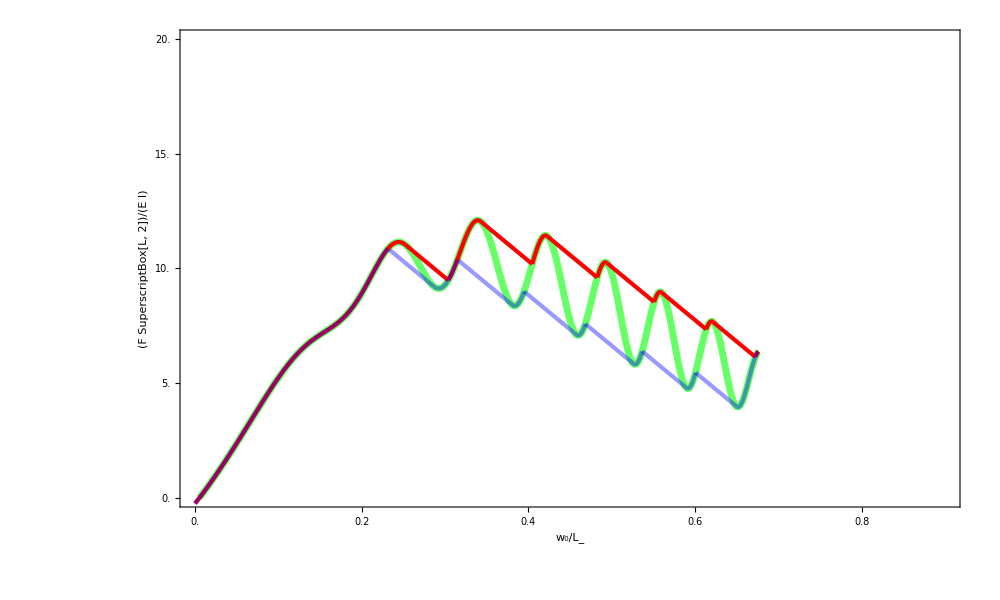

```mathematica
demo = PlotHyster[0.5,0.3,0.04π,0,30]
```

```mathematica
Export["figure/demo.pdf",demo,ImageSize->1000]
```

figure/demo.pdf

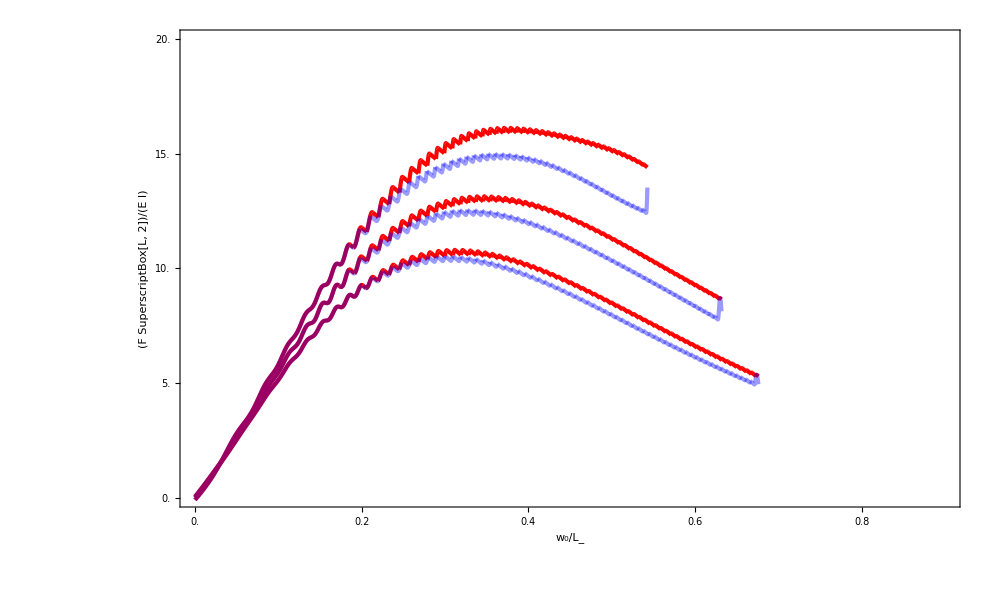

```mathematica
HysteresisPlots=Show[PlotHyster[0.5,0.05,0.004π,0,30],
PlotHyster[0.7,0.05,0.004π,0,30],
PlotHyster[0.9,0.05,0.004π,0,30]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Brown)/Apps/Github/Computational-Solid-Mechanics/ElasticaSolution

```mathematica
Export["Hysteresis.EPS",HysteresisPlots,ImageSize->1000]
```

Hysteresis.EPS

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Hysteresis.PDF"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Hysteresis.EPS"]]]
```